```mathematica
f[x_]:=2^{x-1}+1
g[x_,y_]:=x^2+y^3+4x^2y
```

```mathematica
Sum[1/n^2,{n,1,∞}]
```

π^2/6

```mathematica
Integrate[x^2Sin[2x],{x,0,π}]
```

-π^2/2

```mathematica
Limit[Sin[x]/x,x->0]
```

1

```mathematica
Limit[x^2+y^2,{x,y}->{0,0}]
```

0

```mathematica
f'[x]
```

{2^(-1+x) Log[2]}

```mathematica
D[g[x,y],x,y]
```

8 x

```mathematica
D[g[x,y],{x,2}]
```

2+8 y

```mathematica
Expand[(x+3)(x+2)]
```

6+5 x+x^2

```mathematica
Factor[1+2x+x^2]
```

(1+x)^2

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

1

```mathematica
Solve[x^2+a x+1==0,x]
```

{{x→1/2 (-a-√(-4+a^2))},{x→1/2 (-a+√(-4+a^2))}}

```mathematica
x/.NSolve[x^5-2x+3==0,x, Reals]
```

{-1.42361}

```mathematica
Reduce[x^2+y^2<1,{x,y}]
```

-1<x<1&&-√(1-x^2)<y<√(1-x^2)

```mathematica
FindRoot[Sin[x]+Exp[x],{x,0}]
```

{x→-0.588533}

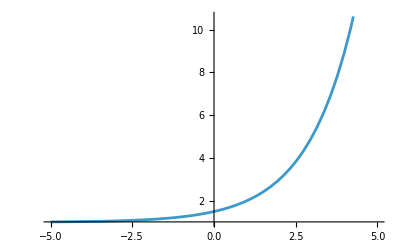

```mathematica
Plot[f[x],{x,-5,5},PlotRange->Automatic]
```

```mathematica
Plot3D[g[x,y],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

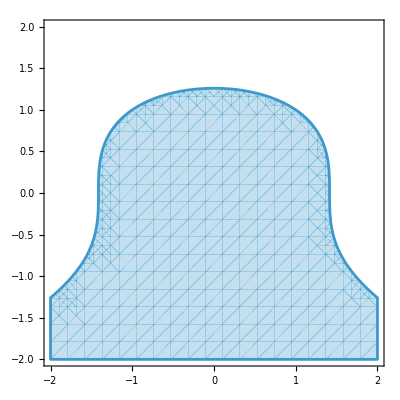

```mathematica
RegionPlot[x^2+y^3<2,{x,-2,2},{y,-2,2}]
```

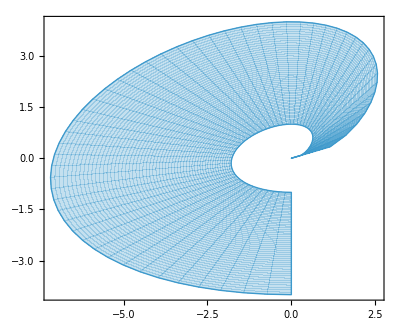

```mathematica
ParametricPlot[r^2{ Sqrt[t]Cos[t], Sin[t]},{t,0,3Pi/2},{r,1,2}]
```

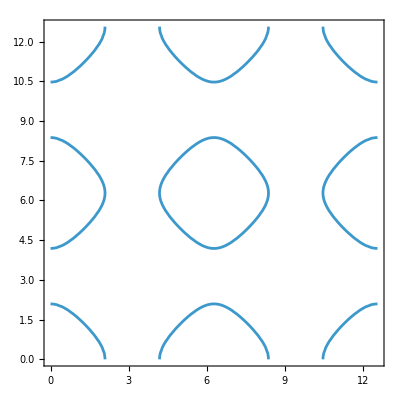

```mathematica
ContourPlot[Cos[x]+Cos[y]==1/2,{x,0,4Pi},{y,0,4Pi}]
```